## Constraint Plots

### Plot the limit

```mathematica
(*Function to convert mass, Log[10,epsilon^{2}]   to   mass, epsilon*)
```

```mathematica
DataConvertermine[data_]:=Table[{data[[i,1]],√(10^data[[i,2]])},{i,Length[data]}]
```

```mathematica
Labelslin={"Br(H->2γ_D)=0.1%","Br(H->2γ_D)=1%","Br(H->2γ_D)=5%","Br(H->2γ_D)=10%","Br(H->2γ_D)=20%","Br(H->2γ_D)=40%"}
```

{Br(H->2γ_D)=0.1%,Br(H->2γ_D)=1%,Br(H->2γ_D)=5%,Br(H->2γ_D)=10%,Br(H->2γ_D)=20%,Br(H->2γ_D)=40%}

```mathematica
DataConvertertest[data_]:=Table[{data[[i,1]],√(10^data[[i,2]])},{i,1,Length[data]}]
```

```mathematica
myopacity=0.5;
```

{{},{0.25,-10.6},{0.35,-11.2},{0.45,-11.46},{0.55,-11.56},{0.65,-11.56},{0.7,-11.46},{0.8,-11.52},{0.85,-11.68},{0.95,-11.83},{1.,-11.87},{1.1,-11.97},{1.2,-12.04},{1.2,-12.04},{1.3,-12.1},{1.4,-12.15},{1.5,-12.2},{1.6,-12.25},{1.7,-12.3},{1.8,-12.36},{1.9,-12.4},{2.,-12.45},{2.,-12.45},{2.1,-12.48},{2.2,-12.52},{2.3,-12.56},{2.4,-12.6},{2.5,-12.64},{2.6,-12.66},{2.7,-12.7}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

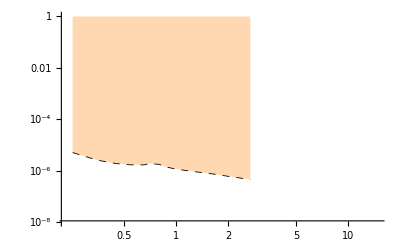

```mathematica
CMS20181part1= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_1_2018data_m0to60_part1.dat","Table"]
CMS20181part1plot = ListLogLogPlot[DataConvertertest[CMS20181part1],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.4]],PlotRange->{10^-8,1}]
```

{{},{3.24,-12.85},{3.34,-12.88},{3.44,-12.91},{3.54,-12.93},{3.64,-12.95},{3.74,-12.96},{3.84,-13.},{3.94,-13.},{4.04,-12.98},{4.14,-13.},{4.24,-13.05},{4.34,-13.06},{4.44,-13.06},{4.54,-13.1},{4.64,-13.12},{4.74,-13.12},{4.84,-13.14},{4.94,-13.17},{5.04,-13.17},{5.14,-13.2},{5.24,-13.2},{5.34,-13.23},{5.44,-13.24},{5.54,-13.26},{5.64,-13.28},{5.74,-13.3},{5.84,-13.3},{5.94,-13.32},{6.04,-13.34},{6.14,-13.36},{6.24,-13.36},{6.34,-13.38},{6.44,-13.4},{6.54,-13.4},{6.64,-13.41},{6.74,-13.44},{6.84,-13.44},{6.94,-13.45},{7.04,-13.48},{7.14,-13.48},{7.24,-13.48},{7.34,-13.5},{7.44,-13.52},{7.54,-13.52},{7.64,-13.53},{7.74,-13.53},{7.84,-13.56},{7.94,-13.56},{8.04,-13.58},{8.14,-13.59},{8.24,-13.6},{8.34,-13.6},{8.44,-13.62},{8.54,-13.62},{8.64,-13.64},{8.74,-13.65},{8.84,-13.66},{8.94,-13.66}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

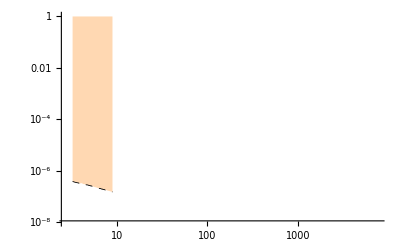

```mathematica
CMS20181part2= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_1_2018data_m0to60_part2.dat","Table"]
CMS20181part2plot = ListLogLogPlot[DataConvertertest[CMS20181part2],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.4]],PlotRange->{10^-8,1}]
```

{{},{11.,-13.84},{11.5,-13.87},{12.,-13.92},{12.5,-13.92},{13.,-13.92},{13.5,-13.98},{14.,-14.04},{14.5,-14.08},{15.,-14.1},{15.5,-14.15},{16.,-14.18},{16.5,-14.22},{17.,-14.24},{17.5,-14.28},{18.,-14.3},{18.5,-14.32},{19.,-14.34},{19.5,-14.36},{20.,-14.38},{20.5,-14.4},{21.,-14.43},{21.5,-14.46},{22.,-14.48},{22.5,-14.5},{23.,-14.52},{23.5,-14.55},{24.,-14.56},{24.5,-14.58},{25.,-14.6},{25.5,-14.64},{26.,-14.67},{26.5,-14.7},{27.,-14.73},{27.5,-14.76},{28.,-14.78},{28.5,-14.82},{29.,-14.84},{29.5,-14.86},{30.,-14.89},{30.5,-14.92},{31.,-14.94},{31.5,-14.96},{32.,-14.99},{32.5,-15.01},{33.,-15.03},{33.5,-15.06},{34.,-15.08},{34.5,-15.1},{35.,-15.11},{35.5,-15.15},{36.,-15.17},{36.5,-15.2},{37.,-15.22},{37.5,-15.25},{38.,-15.28},{38.5,-15.3},{39.,-15.32},{39.5,-15.34},{40.,-15.36},{40.5,-15.38},{41.,-15.4},{41.5,-15.41},{42.,-15.44},{42.5,-15.45},{43.,-15.47},{43.5,-15.49},{44.,-15.5},{44.5,-15.52},{45.,-15.54},{45.5,-15.55},{46.,-15.57},{46.5,-15.58},{47.,-15.6},{47.5,-15.62},{48.,-15.63},{48.5,-15.65},{49.,-15.66},{49.5,-15.68},{50.,-15.69},{50.5,-15.7},{51.,-15.72},{51.5,-15.73},{52.,-15.74},{52.5,-15.75},{53.,-15.76},{53.5,-15.78},{54.,-15.78},{54.5,-15.8},{55.,-15.81},{55.5,-15.83},{56.,-15.84},{56.5,-15.84},{57.,-15.86},{57.5,-15.88},{58.,-15.9},{58.5,-15.91},{59.,-15.93},{59.5,-15.95},{60.,-15.96}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

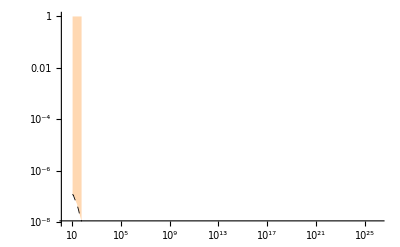

```mathematica
CMS20181part3= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_1_2018data_m0to60_part3.dat","Table"]
CMS20181part3plot = ListLogLogPlot[DataConvertertest[CMS20181part3],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.4]],PlotRange->{10^-8,1}]
```

{{},{0.25,-11.12},{0.35,-11.72},{0.45,-11.98},{0.55,-12.08},{0.65,-12.12},{0.7,-12.08},{0.8,-12.19},{0.85,-12.26},{0.95,-12.38},{1.,-12.42},{1.1,-12.5},{1.2,-12.58},{1.2,-12.58},{1.3,-12.65},{1.4,-12.71},{1.5,-12.76},{1.6,-12.82},{1.7,-12.87},{1.8,-12.92},{1.9,-12.96},{2.,-13.02},{2.,-13.02},{2.1,-13.05},{2.2,-13.09},{2.3,-13.13},{2.4,-13.17},{2.5,-13.2},{2.6,-13.23},{2.7,-13.26}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

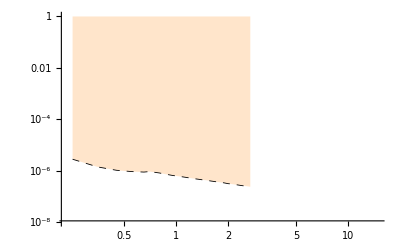

```mathematica
CMS201810part1= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_10_2018data_m0to60_part1.dat","Table"]
CMS201810part1plot = ListLogLogPlot[DataConvertertest[CMS201810part1],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.6]],PlotRange->{10^-8,1}]
```

{{},{3.24,-13.36},{3.34,-13.4},{3.44,-13.4},{3.54,-13.45},{3.64,-13.45},{3.74,-13.48},{3.84,-13.5},{3.94,-13.54},{4.04,-13.54},{4.14,-13.54},{4.24,-13.6},{4.34,-13.6},{4.44,-13.6},{4.54,-13.63},{4.64,-13.67},{4.74,-13.68},{4.84,-13.7},{4.94,-13.7},{5.04,-13.72},{5.14,-13.76},{5.24,-13.76},{5.34,-13.76},{5.44,-13.8},{5.54,-13.8},{5.64,-13.81},{5.74,-13.84},{5.84,-13.84},{5.94,-13.88},{6.04,-13.9},{6.14,-13.9},{6.24,-13.9},{6.34,-13.92},{6.44,-13.95},{6.54,-13.95},{6.64,-13.95},{6.74,-13.99},{6.84,-14.},{6.94,-14.},{7.04,-14.},{7.14,-14.02},{7.24,-14.05},{7.34,-14.05},{7.44,-14.08},{7.54,-14.08},{7.64,-14.1},{7.74,-14.1},{7.84,-14.1},{7.94,-14.12},{8.04,-14.14},{8.14,-14.16},{8.24,-14.17},{8.34,-14.17},{8.44,-14.17},{8.54,-14.2},{8.64,-14.2},{8.74,-14.2},{8.84,-14.2},{8.94,-14.24}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

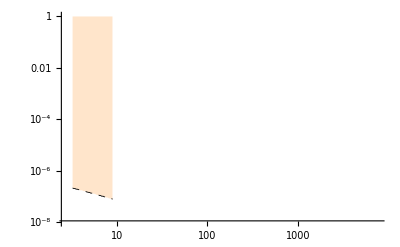

```mathematica
CMS201810part2= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_10_2018data_m0to60_part2.dat","Table"]
CMS201810part2plot = ListLogLogPlot[DataConvertertest[CMS201810part2],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.6]],PlotRange->{10^-8,1}]
```

{{},{11.,-14.4},{11.5,-14.44},{12.,-14.48},{12.5,-14.5},{13.,-14.53},{13.5,-14.56},{14.,-14.6},{14.5,-14.62},{15.,-14.65},{15.5,-14.7},{16.,-14.71},{16.5,-14.74},{17.,-14.8},{17.5,-14.8},{18.,-14.86},{18.5,-14.88},{19.,-14.9},{19.5,-14.9},{20.,-14.96},{20.5,-14.98},{21.,-15.},{21.5,-15.},{22.,-15.04},{22.5,-15.07}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

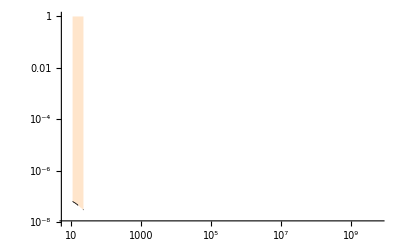

```mathematica
CMS201810part3= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_10_2018data_m0to60_part3.dat","Table"]
CMS201810part3plot = ListLogLogPlot[DataConvertertest[CMS201810part3],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.6]],PlotRange->{10^-8,1}]
```

{{},{0.25,-11.3},{0.7,-12.28},{0.85,-12.46},{1.,-12.6},{1.2,-12.76},{1.7,-13.06},{2.,-13.2},{2.5,-13.4}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

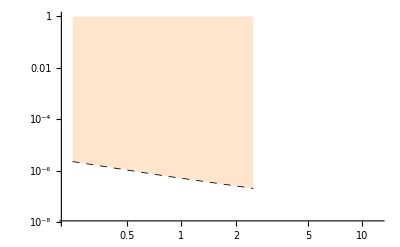

```mathematica
CMS201830part1= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_30_2018data_m0to60_part1.dat","Table"]
CMS201830part1plot = ListLogLogPlot[DataConvertertest[CMS201830part1],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.6]],PlotRange->{10^-8,1}]
```

{{},{3.24,-13.63},{3.74,-13.72},{4.24,-13.84},{4.74,-13.92},{5.24,-14.02},{5.74,-14.1},{6.24,-14.17},{6.74,-14.24},{7.24,-14.3},{7.74,-14.35},{8.24,-14.4},{8.74,-14.48}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

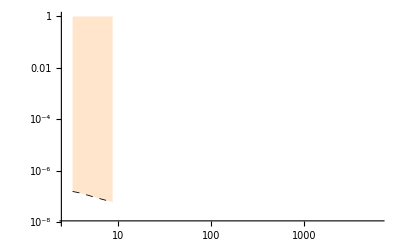

```mathematica
CMS201830part2= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_30_2018data_m0to60_part2.dat","Table"]
CMS201830part2plot = ListLogLogPlot[DataConvertertest[CMS201830part2],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.6]],PlotRange->{10^-8,1}]
```

{{},{11.,-14.65},{12.,-14.72},{13.,-14.8},{14.,-14.88},{15.,-14.93},{16.,-15.},{17.,-15.04},{18.,-15.1},{19.,-15.16},{20.,-15.2},{21.,-15.25},{22.,-15.3},{23.,-15.34},{24.,-15.36},{25.,-15.4},{26.,-15.49},{27.,-15.52},{28.,-15.6},{29.,-15.63},{30.,-15.68},{31.,-15.72},{32.,-15.76},{33.,-15.8},{34.,-15.84},{35.,-15.9},{36.,-15.94},{37.,-16.},{38.,-16.05},{39.,-16.08},{40.,-16.12},{41.,-16.15},{42.,-16.2},{43.,-16.24},{44.,-16.26},{45.,-16.3},{46.,-16.33},{47.,-16.36},{48.,-16.4},{49.,-16.42},{50.,-16.45},{51.,-16.48},{52.,-16.5},{53.,-16.54},{54.,-16.56},{55.,-16.57},{56.,-16.6},{57.,-16.64},{58.,-16.64},{59.,-16.68},{60.,-16.7}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

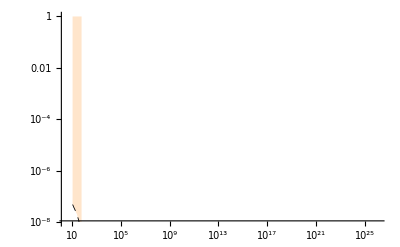

```mathematica
CMS201830part3= Import["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_30_2018data_m0to60_part3.dat","Table"]
CMS201830part3plot = ListLogLogPlot[DataConvertertest[CMS201830part3],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.6]],PlotRange->{10^-8,1}]
```

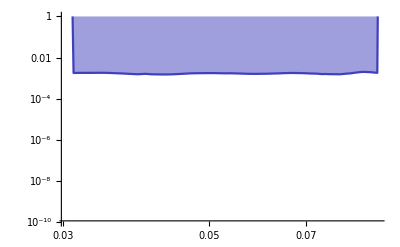

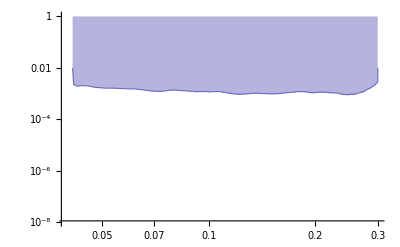

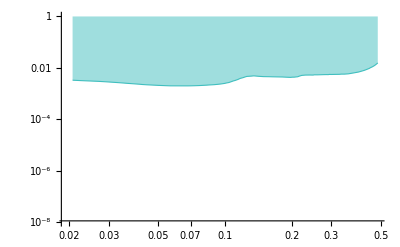

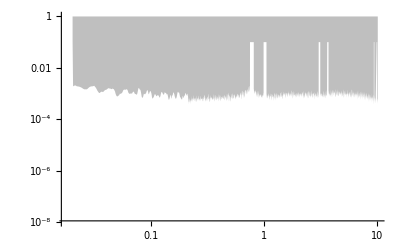

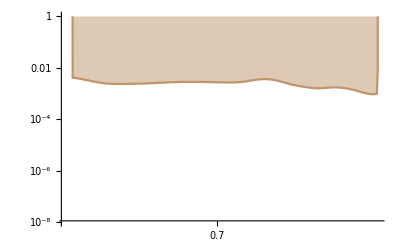

```mathematica
SetDirectory[NotebookDirectory[]];


mμ=0.1057 GeV;
me=0.000511*GeV;
α=1/137.0;
inCM={GeV->5.0677 10^13/CM};
inSec={GeV->1.51926778 10^24/seconds};
SaveRdataMod=Import["data/SaveRdataMod.txt","Table"];

Rhad[m_]:=If[m<.36,0,Interpolation[SaveRdataMod,InterpolationOrder->1][m]]

electronWidthFunction[mA_]:=√(1-4 me^2/(mA^2*GeV^2));
muonWidthFunction[mA_]:=√Max[1-4 mμ^2/(mA^2*GeV^2),0]
totalWidthFunction[mA_]:=√(1-4 me^2/(mA^2*GeV^2))+√Max[1-4 mμ^2/(mA^2*GeV^2),0]  (1+Rhad[mA])
muonfraction[mA_]:=muonWidthFunction[mA]/totalWidthFunction[mA]
SigmaAOnShell[Ecm_,alpha_,alphaD_,epsilon_,mL_,mA_,thetamin_]:=0.3894*10^(-3+15)*4*π*epsilon^2*alpha^2*1/Ecm^2*(1-mA^2/Ecm^2)*((2+(4*mA^2)/(Ecm^2*(1-mA^2/Ecm^2)^2))*Log[2/thetamin]-1+1/8*(2-(4*mA^2)/(Ecm^2*(1-mA^2/Ecm^2)^2))*thetamin^2)
Fmts[label_,color_,{x_,y_},size_,colorbackground_]:=Inset[Style[label,FontSize->size,color],Scaled[{x,y}],Background->colorbackground]
Lifetime[ϵ_,mA_]:=3/(α ϵ^2 mA) 1/totalWidthFunction[mA/GeV];
inCM={GeV->5.0677 10^13/CM};

Clear[DataConverterWithCommaDropper]
DataConverterWithCommaDropper[data_]:=Table[{10^ToExpression[StringDrop[data[[i]][[1]],-1]],10^data[[i,2]]},{i,1,Length[data]}]
(* To convert Subscript[Log, 10] Mass to Mass and Subscript[Log, 10] ϵ  to ϵ: *)
DataConverter[data_]:=Table[{10^data[[i,1]],10^data[[i,2]]},{i,1,Length[data]}]
(* To convert Subscript[Log, 10] Mass to Mass and Subscript[Log, 10] ϵ  to ϵ, and to convert 90% c.l. limit to 95% c.l. limit on epsilon: *)
DataConvertercl90to95[data_]:=Table[{10^data[[i,1]],(2/1.64)^(1/4)10^data[[i,2]]},{i,1,Length[data]}]
(* To convert MeV to GeV and epsilon^2 to epsilon: *)
DataConverter2[data_]:=Table[{data[[i,1]]/1000,√data[[i,2]]},{i,1,Length[data]}]
(* To convert MeV to GeV: *)
DataConverter3[data_]:=Table[{data[[i,1]]/1000,data[[i,2]]},{i,1,Length[data]}]
(* To convert MeV to GeV and epsilon^2 to epsilon, and to convert 90% c.l. limit to 95% c.l. limit on epsilon: *)
DataConverter2cl90to95[data_]:=Table[{data[[i,1]]/1000,(2/1.64)^(1/4)√data[[i,2]]},{i,1,Length[data]}]


myopacity=0.5;
myopacityae=0.3;

mycolor=Blend[{Lighter[Blue],Gray}];
mycolor2=Blend[{Blue,Gray}];

mycolorsn=Blend[{Lighter[Blue],Gray}];
mycolor2sn=Blend[{Blue,Gray}];

mycolore137=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2e137=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolore141=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2e141=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolore774=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2e774=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolororsay=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2orsay=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolorA12011=Blend[{Lighter[Purple],Gray}];
mycolor2A12011=Blend[{Purple,Gray}];

mycolorapex2011=Blend[{Lighter[Purple],Gray}];
mycolor2apex2011=Blend[{Purple,Gray}];

mycolorU70=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2U70=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolorcharm=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2charm=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolorKLOE2012conservative=Blend[{Lighter[Orange],Gray}];
mycolor2KLOE2012conservative=Blend[{Orange,Gray}];

mycolorKLOE2012optimistic=Blend[{Lighter[Orange],Gray}];
mycolor2KLOE2012optimistic=Blend[{Orange,Gray}];

mycolorLHCb2018 = Blend[{Lighter[Blue],Lighter[Purple]}];

(*mycolorBabar1=Blend[{Lighter[Orange],Gray}];
mycolor2Babar1=Blend[{Orange,Gray}];*)

mycolorBabar1=Gray;
mycolor2Babar1=Gray;

mycoloraμlimit5σ=Blend[{Lighter[Cyan],Gray}];
mycolor2aμlimit5σ=Blend[{Cyan,Gray}];

mycoloraμ2σBand=Blend[{Green,Gray}];
mycolor2aμ2σBand=Blend[{Darker[Green],Gray}];

mycolorae95clLimit=Blend[{Lighter[Red],Gray}];
mycolor2ae95clLimit=Blend[{Red,Gray}];

mycolorlsnd=Lighter[Lighter[Gray]];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2lsnd=Lighter[Lighter[Gray]];(*Blend[{Orange,Gray}];*)

mycolorwasacosy2010=Blend[{Lighter[Orange],Gray}];
mycolor2wasacosy2010=Blend[{Orange,Gray}];

mycolormodelindependent=Blend[{Lighter[Orange],Gray}];
mycolor2modelindependent=Blend[{Orange,Gray}];


sn=Import["data/SN.txt","Table"];
sn1=Take[sn,{1,38}];
sn2=Take[sn,{39,Length[sn]}];
snplot=ListLogLogPlot[{sn1,sn2},Joined->True,PlotStyle->{mycolorsn,mycolorsn},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolor]];
snplotL=ListLogLogPlot[{sn1,sn2},Joined->True,PlotStyle->{mycolor2sn,mycolor2sn}];



e137=Import["data/E137_Andreas.dat","Table"];
e1371=Take[DataConverterWithCommaDropper[e137],{1,352}];
e1372=Sort[Take[DataConverterWithCommaDropper[e137],{353,Length[e137]}]];
e137plot=ListLogLogPlot[{e1371,e1372},Joined->True,PlotStyle->{mycolore137,mycolore137},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolore137]];
e137plotL=ListLogLogPlot[{e1371,e1372},Joined->True,PlotStyle->{mycolor2e137,mycolor2e137}];



e141=Import["data/E141_Andreas.dat","Table"];
e1411=Take[DataConverterWithCommaDropper[e141],{1,186}];
e1412=Sort[Take[DataConverterWithCommaDropper[e141],{187,Length[e141]}]];
e141plot=ListLogLogPlot[{e1411,e1412},Joined->True,PlotStyle->{mycolore141,mycolore141},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolore141]];
e141plotL=ListLogLogPlot[{e1411,e1412},Joined->True,PlotStyle->{mycolor2e141,mycolor2e141}];



e774=Import["data/E774_Andreas.dat","Table"];
e7741=Take[DataConverterWithCommaDropper[e774],{1,144}];
e7742=Sort[Take[DataConverterWithCommaDropper[e774],{145,Length[e774]}]];
e774plot=ListLogLogPlot[{e7741,e7742},Joined->True,PlotStyle->{mycolore774,mycolore774},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolore774]];
e774plotL=ListLogLogPlot[{e7741,e7742},Joined->True,PlotStyle->{mycolor2e774,mycolor2e774}];



orsay=Import["data/Orsay_Andreas.dat","Table"];
orsay1=Take[DataConverterWithCommaDropper[orsay],{1,276}];
orsay2=Sort[Take[DataConverterWithCommaDropper[orsay],{277,Length[orsay]}]];
orsayplot=ListLogLogPlot[{orsay1,orsay2},Joined->True,PlotStyle->{mycolororsay,mycolororsay},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolororsay]];
orsayplotL=ListLogLogPlot[{orsay1,orsay2},Joined->True,PlotStyle->{mycolor2orsay,mycolor2orsay}];




(* Convert MAMI limit from 90% c.l. to 95% c.l. on epsilon by multiplying by (2/1.64)^(1/4), i.e. using DataConvertercl90to95 *)
A12011=DataConvertercl90to95[Import["data/A1_2011.dat","Table"]];
A12011plot=ListLogLogPlot[A12011,Joined->True,PlotStyle->mycolorA12011,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorA12011]];
A12011plotL=ListLogLogPlot[A12011,Joined->True,PlotStyle->mycolor2A12011];




U70=Join[Import["data/U70-Serpukhov.txt","Table"],{{0.13889,4.9088072777*^-7}}];(* added a point at the end to close curve properly *)
U701=Take[U70,{1,33}];
U702=Take[U70,{34,Length[U70]}];
U70plot=ListLogLogPlot[{U701,U702},Joined->True,PlotStyle->{mycolorU70,mycolorU70},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolorU70]];
U70plotL=ListLogLogPlot[{U701,U702},Joined->True,PlotStyle->{mycolor2U70,mycolor2U70}];




KLOE2012conservative=DataConverter2[Import["data/KLOE-conservative.txt","Table"]];
KLOE2012conservativeplot=ListLogLogPlot[KLOE2012conservative,Joined->True,PlotStyle->mycolorKLOE2012conservative,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorKLOE2012conservative]];
KLOE2012conservativeplotL=ListLogLogPlot[KLOE2012conservative,Joined->True,PlotStyle->mycolor2KLOE2012conservative];




KLOE2012optimistic=DataConverter2[Import["data/KLOE-optimistic.txt","Table"]];
KLOE2012optimisticplot=ListLogLogPlot[KLOE2012optimistic,Joined->True,PlotStyle->mycolorKLOE2012optimistic,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorKLOE2012optimistic]];
KLOE2012optimisticplotL=ListLogLogPlot[KLOE2012optimistic,Joined->True,PlotStyle->mycolor2KLOE2012optimistic];



(* LHCb limit 2017 paper https://journals.aps.org/prl/abstract/10.1103/PhysRevLett.120.061801*)

LHCb2018 = DataConverter2[Import["data/prompt-excluded_LHCb2018.txt","Table"]];
LHCb2018plot = ListLogLogPlot[LHCb2018,Joined->True,PlotStyle->mycolorLHCb2018,Filling->{1->Top},
FillingStyle->Directive[Opacity[myopacity],mycolorLHCb2018]];


(* LHCb limit 2017 paper https://journals.aps.org/prl/abstract/10.1103/PhysRevLett.120.061801*)

LHCb2018longlived1 = DataConverter2[Import["data/long-lived-excluded_LHCb2018_region1.txt","Table"]];
LHCb2018longlived1plot = ListLogLogPlot[LHCb2018longlived1,Joined->True,PlotStyle->mycolorLHCb2018,Filling->{1->Top},
FillingStyle->Directive[Opacity[myopacity],mycolorLHCb2018]];

LHCb2018longlived2 = DataConverter2[Import["data/long-lived-excluded_LHCb2018_region2.txt","Table"]];
LHCb2018longlived2plot = ListLogLogPlot[LHCb2018longlived2,Joined->True,PlotStyle->mycolorLHCb2018,Filling->{1->Top},
FillingStyle->Directive[Opacity[myopacity],mycolorLHCb2018]];

LHCb2018longlived3 = DataConverter2[Import["data/long-lived-excluded_LHCb2018_region3.txt","Table"]];
LHCb2018longlived3plot = ListLogLogPlot[LHCb2018longlived3,Joined->True,PlotStyle->mycolorLHCb2018,Filling->{1->Top},
FillingStyle->Directive[Opacity[myopacity],mycolorLHCb2018]];

LHCb2018longlived4 = DataConverter2[Import["data/long-lived-excluded_LHCb2018_region4.txt","Table"]];
LHCb2018longlived4plot = ListLogLogPlot[LHCb2018longlived4,Joined->True,PlotStyle->mycolorLHCb2018,Filling->{1->Top},
FillingStyle->Directive[Opacity[myopacity],mycolorLHCb2018]];


(* 90% BR limit from 0902.2176: *)
(* Do 200 MeV -- 1 GeV data approximately accurately, but then add a few data points at the end that roughly interpolates among the BaBar results *)
BabarBR=Join[Import["data/Babar-1.txt","Table"],{{1.,10.^-6},{4.,10.^-6},{9.3,3. 10^-6}}];
(* No of events that BaBar is sensitive to equals (121.8±1.2)×10^6 Upsilon(3S) decays times Branching Ratio Constraint in 0902.2176 *)
(* Convert from 90% c.l. limit to 95% c.l. limit on epsilon by multiplying by (2/1.64)^(1/4) *)
Babar1=Table[{BabarBR[[i,1]],(2/1.64)^(1/4)√((BabarBR[[i,2]]*121.8 10^6)/(30*SigmaAOnShell[10.58,1/137.0,1,1.0(*epsilon*),1.0,BabarBR[[i,1]],ArcCos[0.9]]*muonfraction[BabarBR[[i,1]]]))},{i,1,Length[BabarBR]}];
Babar1plot=ListLogLogPlot[Babar1,Joined->True,PlotRange->{10^-4,10^-1},PlotStyle->mycolorBabar1,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorBabar1]];
Babar1plotL=ListLogLogPlot[Babar1,Joined->True,PlotStyle->mycolor2Babar1];




(* Convert APEX limit from 90% c.l. to 95% c.l. on epsilon by multiplying by (2/1.64)^(1/4), i.e. using DataConverter2cl90to95 *)
apex2011=Join[{{0.177024,0.01}},DataConverter2cl90to95[Import["data/epsilon_PCL_6_30_10_27.txt","Table"]],{{0.249776,0.01}}]; (* added point at beginning and end to make curve go up to 10^-2 *)
apex2011plot=ListLogLogPlot[apex2011,Joined->True,PlotStyle->mycolorapex2011,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorapex2011]];
apex2011plotL=ListLogLogPlot[apex2011,Joined->True,PlotStyle->mycolor2apex2011];




(* anomalous magnetic moment of muon: g-2 (constraint taken from Pospelov (arXiv:0811.1030[hep-ph]))*)
gminus2[alpha_,ϵ_,mA_,ml_]:=alpha/(2*π)*ϵ^2*NIntegrate[(2*ml^2*z*(1-z)^2)/(ml^2*(1-z)^2+mA^2*z),{z,0,1}]
(*use results from: 1010.4180, Eq. 22 and following paragraph; based on e+e- data, gives 3.6-sigma;  numbers here are in units of 10^-10
Subscript[a, SM] = 11659180.2 ± 4.2 ± 2.6 ± 0.2 (4.9)
Subscript[a, exp] = 11 659 208.9 ± 5.4 ± 3.3
Difference is 28.7 ± 8.0 (3.6 σ)*)

aμlimit5σ=Table[{masses,√(((28.7+5*8.0)*10^-10)/gminus2[1/137,1.,masses,mμ/GeV])},{masses,0.001,5.0,0.01}];
aμ2σHigh=Table[{masses,√(((28.7+2*8.0)*10^-10)/gminus2[1/137,1.,masses,mμ/GeV])},{masses,0.001,8.0,0.01}];
aμ2σLow=Table[{masses,√(((28.7-2*8.0)*10^-10)/gminus2[1/137,1.,masses,mμ/GeV])},{masses,0.001,8.0,0.01}];



aμlimit5σplot=ListLogLogPlot[aμlimit5σ,Joined->True,PlotStyle->mycoloraμlimit5σ,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycoloraμlimit5σ]];
aμlimit5σplotL=ListLogLogPlot[aμlimit5σ,Joined->True,PlotStyle->mycolor2aμlimit5σ];
aμ2σBandplot=ListLogLogPlot[{aμ2σLow,aμ2σHigh},Joined->True,PlotStyle->mycoloraμ2σBand,Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycoloraμ2σBand]];
aμ2σBandplotL=ListLogLogPlot[{aμ2σLow,aμ2σHigh},Joined->True,PlotStyle->mycoloraμ2σBand];




(*Electron anomaous magnetic moment:
Discrepancy between Experimental Measurement and Standard Model is: 
Subscript[Δa, e] = Subscript[a, exp]-Subscript[a, SM] = -1.06 (0.82) × 10^-12*)
ae90clLimit=Table[{masses,√(((-1.06+1.64*0.82)*10^-12)/gminus2[1/137,1.,masses,me/GeV])},{masses,0.001,1.0,0.01}];
ae90cllimitplot=ListLogLogPlot[ae90clLimit,Joined->True,PlotStyle->mycolor,Filling->{1->Top},FillingStyle->mycolor,PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae90cllimitplotL=ListLogLogPlot[ae90clLimit,Joined->True,PlotStyle->{mycolor2ae95clLimit,Dashed},PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae95clLimit=Table[{masses,√(((-1.06+2*0.82)*10^-12)/gminus2[1/137,1.,masses,me/GeV])},{masses,0.001,5.0,0.01}];
ae95cllimitplot=ListLogLogPlot[ae95clLimit,Joined->True,PlotStyle->mycolorae95clLimit,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacityae],mycolorae95clLimit],PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae95cllimitplotL=ListLogLogPlot[ae95clLimit,Joined->True,PlotStyle->mycolor2ae95clLimit,PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae3σLimit=Table[{masses,√(((-1.06+3*0.82)*10^-12)/gminus2[1/137,1.,masses,me/GeV])},{masses,0.001,1.0,0.01}];
ae3σlimitplot=ListLogLogPlot[ae3σLimit,Joined->True,PlotStyle->mycolor,Filling->{1->Top},FillingStyle->mycolor,PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae3σlimitplotL=ListLogLogPlot[ae3σLimit,Joined->True,PlotStyle->{mycolor2ae95clLimit,DotDashed},PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae5σLimit=Table[{masses,√(((-1.06+5*0.82)*10^-12)/gminus2[1/137,1.,masses,me/GeV])},{masses,0.001,1.0,0.01}];
ae5σlimitplot=ListLogLogPlot[ae5σLimit,Joined->True,PlotStyle->mycolor,Filling->{1->Top},FillingStyle->mycolor,PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae5σlimitplotL=ListLogLogPlot[ae5σLimit,Joined->True,PlotStyle->{mycolor2ae95clLimit,Dotted},PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];

mycolorae3σLimit2014=Blend[{Lighter[Red],Gray}];
ae3σLimit2014=Import["data2014/ae3σLimit.txt","Table"];
ae3σlimitplot2014=ListLogLogPlot[ae3σLimit2014,Joined->True,PlotStyle->mycolorae3σLimit2014,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacityae],mycolorae3σLimit2014],PlotRange->{{0.001,1},{10^-6,1}},Frame->True];



lsnd=Import["data/lsnd.txt","Table"];
lsnd1=Join[Take[lsnd,{1,41}],{{0.2004062831,2.9850926399*^-7}}]; (* add a point to make curve smooth *)
lsnd2=Sort[Take[lsnd,{42,Length[lsnd]}]];
lsndplot=ListLogLogPlot[{lsnd1,lsnd2},Joined->True,PlotStyle->{mycolorlsnd,mycolorlsnd},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolorlsnd]];
lsndplotL=ListLogLogPlot[{lsnd1,lsnd2},Joined->True,PlotStyle->{mycolor2lsnd,mycolor2lsnd}];




wasacosy2010=Join[{{0.0013065973520000002,0.1}},DataConverter2[Import["data/wasa-cosy.txt","Table"]],{{0.0983349304199,0.1}}] ;(* added first and last point to make curve go to axis nicely*)
wasacosy2010plot=ListLogLogPlot[wasacosy2010,Joined->True,PlotStyle->mycolorwasacosy2010,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorwasacosy2010]];
wasacosy2010plotL=ListLogLogPlot[wasacosy2010,Joined->True,PlotStyle->mycolor2wasacosy2010];




modelindependent=Import["data/model-independent.txt","Table"];
modelindependentplot=ListLogLogPlot[modelindependent,Joined->True,PlotStyle->mycolormodelindependent,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolormodelindependent]];
modelindependentplotL=ListLogLogPlot[modelindependent,Joined->True,PlotStyle->mycolor2modelindependent];



charm=DataConverter3[Import["data/charm.txt","Table"]];
charm1=Join[{{0.001,10^-5.95}},Take[charm,{1,33}]];(*added point somewhat arbitrarily to extend plot to 1 MeV*)
charm2=Join[{{0.001,0.0004}},Take[charm,{34,Length[charm]}]];(*added point somewhat arbitrarily to extend plot to 1 MeV*)

(* CONVERT THE LOWER LINE FROM A 90% C.L. UPPER LIMIT (BASED ON 2.3 EVENTS OBSERVED IN 1204.3583) TO A 95% C.L. UPPER LIMIT BASED ON A FELDMAN COUSINS NUMBER OF 3.09 EVENTS; CAN ONLY DO THIS FOR LOWER LINE, SINCE UPPER LINE IS LIMITED BY LIFETIME NOT BY STATISTICS *)
charm1=Table[{charm1[[i,1]],√(3.09/2.3)charm1[[i,2]]},{i,1,Length[charm1]}];
charmplot=ListLogLogPlot[{charm1,charm2},Joined->True,PlotStyle->{mycolorcharm,mycolorcharm},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolorcharm]];
charmplotL=ListLogLogPlot[{charm1,charm2},Joined->True,PlotStyle->{mycolor2charm,mycolor2charm}];





myPhenix=Blend[{Blue,Gray}];
phenix2014=Join[{{0.031,1}},DataConverter2cl90to95[Import["data2014/Phenix2014.txt","Table"]],{{0.09,1}}];(* added point at beginning and end to make curve go up to 10^-1 *)
phenix2014plot=ListLogLogPlot[phenix2014,Joined->True,PlotStyle->myPhenix,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],myPhenix],PlotRange->{10^-10,1}];

phenix2014plot


Mainz2014Data=Import["data2014/Mainz-2014.txt","Table"];
Mainz2014Data2=Table[{Mainz2014Data[[i,1]],√Mainz2014Data[[i,2]]},{i,1,Length[Mainz2014Data]}];
Mainz2014Plot=ListLogLogPlot[Mainz2014Data2,Joined->True,PlotStyle->{Blend[{Gray,Lighter[Blue]}],Thickness[0.002]},Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],Blend[{Gray,Lighter[Blue]}]]];

Mainz2014Plot

Hades2013Data=Import["data2014/Hades.txt","Table"];
Hades2013Data2=Table[{Hades2013Data[[i,1]],(1.96/1.64)^(1/2)√Hades2013Data[[i,2]]},{i,1,Length[Hades2013Data]}];
Hades2013Plot=ListLogLogPlot[Hades2013Data2,Joined->True,PlotStyle->{Blend[{Cyan,Gray}],Thickness[0.002]},Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],Blend[{Cyan,Gray}]]];

Hades2013Plot


babar2014Data=Import["data2014/BabarNew95.txt","Table"];
babar2014PlotL=ListLogLogPlot[babar2014Data,Joined->True,PlotStyle->{Thickness[0.005],(*Blend[{Orange,Gray}]*)Gray},PlotRange->{10^-10,1}];
babar2014Plot=ListLogLogPlot[babar2014Data,Joined->True,PlotStyle->{(*Blend[{Orange,Gray}]*)Gray,Thickness[0.0001]},Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],(*Blend[{Orange,Gray}]*)Gray]];
babar2014Plot2=ListLogLogPlot[babar2014Data,Joined->True,PlotStyle->None,Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],(*Blend[{Orange,Gray}]*)Gray]];
babar2014PlotNoLines=ListLogLogPlot[babar2014Data,Joined->True,PlotStyle->None,Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],(*Blend[{Orange,Gray}]*)Gray]];

babar2014PlotNoLines



KLOE2014=Import["data2014/KLOE-2014.txt","Table"];
KLOE20142=DataConverter2cl90to95[Join[{{517.9,1}},KLOE2014,{{979.9,1}}]]; (*added point at beginning and end to make it go to 1*)
KLOE2014plot=ListLogLogPlot[KLOE20142,Joined->True,PlotStyle->{mycolorKLOE2012optimistic},Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],Blend[{Lighter[Orange],Gray}]]];

KLOE2014plot
```

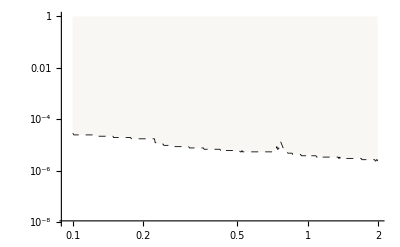

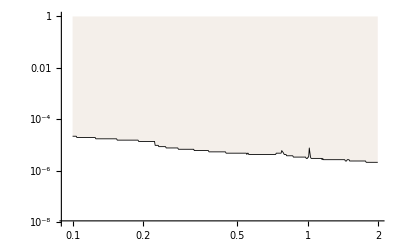

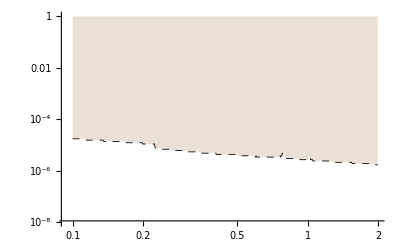

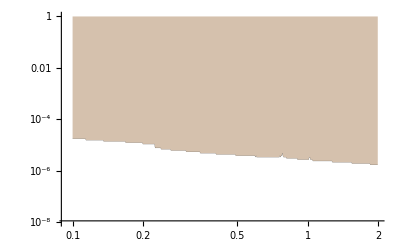

```mathematica
ATLAS05prompt = Import["data/ATLAS05.txt","Table"];
ATLAS05promptplot =  ListLogLogPlot[ATLAS05prompt,Joined->True,PlotStyle->{(*Lighter[Brown,0.9]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.9]],PlotRange->{10^-8,1}]
ATLAS10prompt = Import["data/ATLAS10.txt","Table"];
ATLAS10promptplot =  ListLogLogPlot[ATLAS10prompt,Joined->True,PlotStyle->{(*Lighter[Brown,0.8]*)Black,Thickness[0.0015]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.8]],PlotRange->{10^-8,1}]
ATLAS20prompt = Import["data/ATLAS20.txt","Table"];
ATLAS20promptplot =  ListLogLogPlot[ATLAS20prompt,Joined->True,PlotStyle->{(*Lighter[Brown,0.6]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.6]],PlotRange->{10^-8,1}]
ATLAS40prompt = Import["data/ATLAS40.txt","Table"];
ATLAS40promptplot =  ListLogLogPlot[ATLAS20prompt,Joined->True,PlotStyle->{(*Lighter[Brown,0.2]*)Black,Thickness[0.0001]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.2]],PlotRange->{10^-8,1}]
```

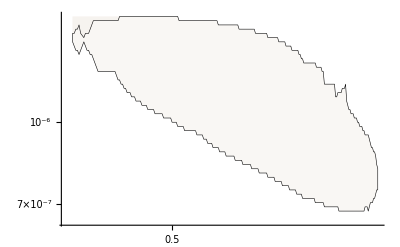

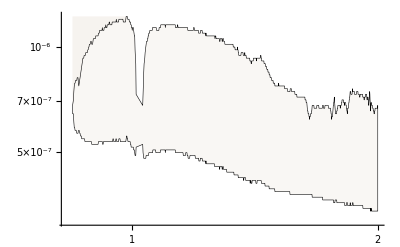

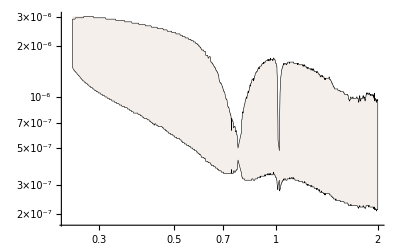

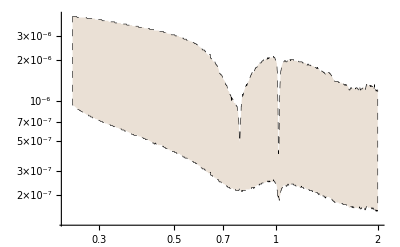

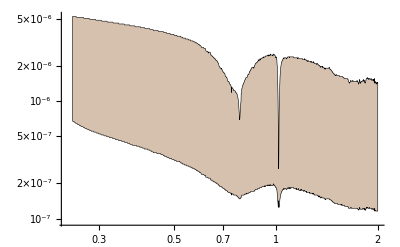

```mathematica
ATLAS20145a = Import["data2014/g_ATLAS5a.txt","Table"];
ATLAS20145aplot = ListLogLogPlot[ATLAS20145a,Joined->True,PlotStyle->{(*Lighter[Brown,0.9]*)Black,Thickness[0.0010]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.9]]]
ATLAS20145b = Import["data2014/g_ATLAS5b.txt","Table"];
ATLAS20145bplot = ListLogLogPlot[ATLAS20145b,Joined->True,PlotStyle->{(*Lighter[Brown,0.9]*)Black,Thickness[0.0010]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.9]]]
ATLAS201410 = Import["data2014/g_ATLAS10.txt","Table"];
ATLAS201410plot = ListLogLogPlot[ATLAS201410,Joined->True,PlotStyle->{(*Lighter[Brown,0.8]*)Black,Thickness[0.0010]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.8]]]
ATLAS201420 = Import["data2014/g_ATLAS20.txt","Table"];
ATLAS201420plot = ListLogLogPlot[ATLAS201420,Joined->True,PlotStyle->{(*Lighter[Brown,0.6]*)Black,Thickness[0.0010],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.6]]]
ATLAS201440 = Import["data2014/g_ATLAS40.txt","Table"];
ATLAS201440plot = ListLogLogPlot[ATLAS201440,Joined->True,PlotStyle->{(*Lighter[Brown,0.2]*)Black,Thickness[0.0010]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.2]]]
```

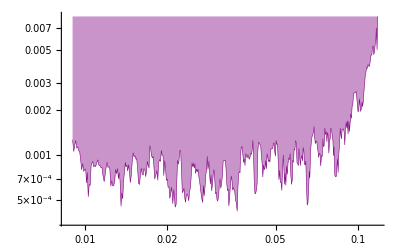

```mathematica
NA48 = Import["data/NA48.txt","Table"];
NA48plot = ListLogLogPlot[NA48,Joined->True,PlotStyle->{(*Lighter[Brown,0.2]*)Purple,Thickness[0.0010]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Blend[{Lighter[Purple],Purple}]]]
```

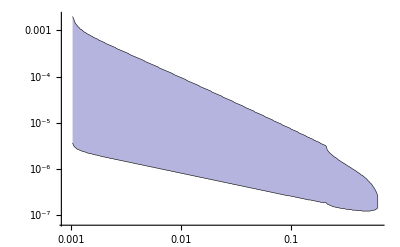

General::stop: Further output of ListLogLogPlot::lpn will be suppressed during this calculation.

ListLogLogPlot::lpn: Null is not a list of numbers or pairs of numbers.

Import::nffil: File not found during Import.

Blend::arg: RGBColor[0, 1, 1] is not a valid list of colors or images, or pairs of a real number and a color or an image.

Import::nffil: File not found during Import. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/Import/nffil",
ButtonNote->"Import::nffil"]

```mathematica
nucal = Import["data/nucaltemp2.txt","Table"];
nucalplot = ListLogLogPlot[nucal,Joined->True,PlotStyle->{(*Lighter[Brown,0.2]*)Black,Thickness[0.0010],solid},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Blend[{Lighter[Blue],Gray}]]]
```

```mathematica
Clear[fticksR,fticksR2,fticksR3,PrettyExp,PrettyExpR2]
PrettyExp[x_,MAX_:2]:=If[Abs[x]≥MAX,Superscript[10,x],If[x≥0,10^x,10.^x]]
(* Axis for Epsilon versus mass: *)
fticksR[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
PrettyExpR2[x_,MAX_:2]:=If[Abs[x]>MAX,Superscript[10,2x],If[x≥0,10^x,10.^x]]
(* Axis for Epsilon^2 versus mass *)fticksR2[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]
(* Axis for Epsilon^2 versus mass, but with y-axis labels only every 2 decades *)
fticksR3[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]/2),10.^(0.5+x+Log[10,i-10]/2)]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1}],1]
```

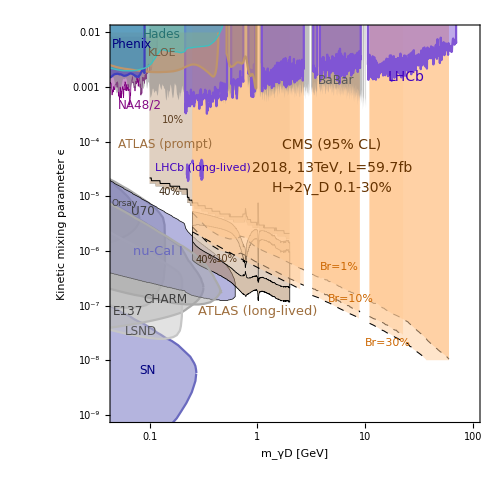

Export::nodir: Directory C:\Users\alfre\Documents\GitHub\DarkPhoton_Limits\plots\ does not exist.

Export::noopen: Cannot open plots/AllConstraints-11-14-12.pdf.

```mathematica
mylegendplot9GeV=LogLogPlot[1,{m,0.001,100},Frame->True,PlotRange->{{0.05,100},{10^-9,0.99 10^-2}},FrameTicks->{Automatic,(*fticks2[10^-11,10^-1,1]*)(*fticksR[10^-11,10^-2,0]*)Automatic},FrameLabel->{Row[{Spacer@315,"m_γD [GeV]"}],Row[{Spacer@150,"Kinetic mixing parameter ϵ"}]},LabelStyle->22,
Epilog->{
(*Inset[Style["Orsay",FontSize->12,Black],Scaled[{0.3,0.59}]],*)
(* 95% c.l. *) Inset[Style["U70",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.089,0.53}]],
(* 95% c.l. *) Inset[Style["Orsay",FontSize->9,Blend[{Gray,Black}]],Scaled[{0.040,0.55}]],
(* 95% c.l. *) Inset[Style["E137",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.05,0.28}]],
(* 95% c.l. *) (*Inset[Style["E141",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.05,0.8}]],*)
(* 95% c.l. *)(*Inset[Style["E774",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.07,0.87}]],*)
(* 95% c.l. *) Inset[Style["CHARM",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.15,0.31}]],
(* 95% c.l. *) Inset[Style["nu-Cal I",FontSize->13, Blend[{Lighter[Blue],Gray}]],Scaled[{0.13,0.43}]],
(* 5σ c.l. *) (*Inset[Style["a_(μ,  5 σ)",FontSize->12,Blend[{Cyan,Black}]],Scaled[{0.2,0.96}]],*)
(* 95% c.l. band *)(*Inset[Rotate[Style["a_(μ, ±2σ) favored",FontSize->12,Blend[{Green,Black}]],5°],Scaled[{0.11,0.89}]],*)
(* 95% c.l. *)Inset[Style["Phenix",FontSize->12,Blend[{Blue,Black}]],Scaled[{0.06,0.95}]],
(* 95% c.l. *)Inset[Style["Hades",FontSize->12,Darker[Blend[{Cyan,Gray}],0.4]],Scaled[{0.14,0.975}]],
(* 95% c.l. *)(*Inset[Style["a_e",FontSize->12,Blend[{Red,Black}]],Scaled[{0.1,0.86}]],*)
(* 95% c.l. *) Inset[Style["BaBar",FontSize->12, Darker[Gray,0.3]],Scaled[{0.61,0.86}]],
(* 95% c.l. *) Inset[Style["CMS (95% CL)",FontSize->14,Darker[Orange,0.6]],Scaled[{0.60,0.70}]],
(* 95% c.l. *) Inset[Style["2018, 13TeV, L=59.7fb",FontSize->14,Darker[Orange,0.6]],Scaled[{0.60,0.64}]],
(* 95% c.l. *) Inset[Style["H→2γ_D 0.1-30%",FontSize->14,Darker[Orange,0.6]],Scaled[{0.60,0.59}]],
(* 95% c.l. *) Inset[Style["LHCb",FontSize->14,Blend[{Blue,Purple}]],Scaled[{0.80,0.87}]],
(* 95% c.l. *) Inset[Style["LHCb (long-lived)",FontSize->11,Blend[{Blue,Purple}]],Scaled[{0.25,0.64}]],
(*Inset[Style["0.1%",FontSize->12,(*Blend[{Purple,Black}]*)Darker[Orange,0.5]],Scaled[{0.22,0.70}]],*)
Inset[Style["Br=1%",FontSize->11,(*Blend[{Purple,Black}]*)Darker[Orange,0.2]],Scaled[{0.62,0.39}]],
Inset[Style["Br=10%",FontSize->11,(*Blend[{Purple,Black}]*)Darker[Orange,0.2]],Scaled[{0.65,0.31}]],
Inset[Style["Br=30%",FontSize->11,(*Blend[{Purple,Black}]*)Darker[Orange,0.2]],Scaled[{0.75,0.20}]],
(* 95% c.l. *) Inset[Style["ATLAS (long-lived)",FontSize->13,Lighter[Brown,0.05]],Scaled[{0.40,0.28}]],
(* 95% c.l. *) Inset[Style["ATLAS (prompt)",FontSize->12,Lighter[Brown,0.05]],Scaled[{0.15,0.70}]],
(* 95% c.l. *) Inset[Style["NA48/2",FontSize->12,Lighter[Purple,0.05]],Scaled[{0.08,0.80}]],
Inset[Style["40%",FontSize->10,(*Blend[{Purple,Black}]*)Darker[Brown,0.6]],Scaled[{0.26,0.41}]],
Inset[Style["40%",FontSize->10,(*Blend[{Purple,Black}]*)Darker[Brown,0.6]],Scaled[{0.16,0.58}]],
Inset[Style["10%",FontSize->10,(*Blend[{Purple,Black}]*)Darker[Brown,0.4]],Scaled[{0.315,0.412}]],
Inset[Style["10%",FontSize->10,(*Blend[{Purple,Black}]*)Darker[Brown,0.4]],Scaled[{0.17,0.762}]],
(*Inset[Style["5%",FontSize->11,(*Blend[{Purple,Black}]*)Darker[Brown,0.2]],Scaled[{0.27,0.425}]],*)
(* 95% c.l. *) (*Inset[Style["√s=13 TeV",FontSize->14,FontFamily->"Arial",Darker[Orange,0.6]],Scaled[{0.52,0.63}]],*)
(*(* 95% c.l. *) Inset[Style["pp→h→2n_1→2γ_D+2n_D→4μ+X",FontSize->18,FontFamily->"Arial",Blend[{Black,Black}]],Scaled[{0.60,0.15}]],*)
(* 95% c.l. *) Inset[Style["KLOE",FontSize->11,Darker[mycolorKLOE2012optimistic,0.4]],Scaled[{0.14,0.93}]],
(* 95% c.l. *) Inset[Style["SN",FontSize->12,Blend[{Blue,Black}]],Scaled[{0.10,0.13}]],
(* 95% c.l. *) Inset[Style["LSND",FontSize->12,Blend[{Lighter[Gray],Black}]],Scaled[{0.085,0.23}]],
(*(* 95% c.l. *) Inset[Style["APEX/MAMI",FontSize->8,Blend[{Purple,Black}],Background->None],Scaled[{0.13,0.89}]],*)
(*(* 95% c.l. *) Inset[Style["Test Runs",FontSize->8,Blend[{Purple,Black}],Background->None],Scaled[{0.13,0.86}]]*)
 (*Inset[Style["Test Runs",FontSize->9,Blend[{Purple,Black}],Background->None],Scaled[{0.13,0.86}]]*)
(* 95% c.l. *) (*Inset[Style["Orsay",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.05,0.75}]]*)
}];
(*mycomboplot9GeV=Show[mylegendplot9GeV,ATLAS201440plot,(*ATLAS201420plot,*)ATLAS201410plot,ATLAS20145aplot,ATLAS20145bplot,(*CMS201420plot*),(*CMS20145plot,*),LHCb2018plot,LHCb2018longlived1plot,LHCb2018longlived2plot,LHCb2018longlived3plot,LHCb2018longlived4plot,aμ2σBandplot,aμlimit5σplot,snplot,e137plot,e141plot,e774plot,orsayplot,U70plot,KLOE2012conservativeplot(*,KLOE2012optimisticplot*),(*Babar1plot*)babar2014PlotNoLines,A12011plot,apex2011plot,(*ae90cllimitplot,*)lsndplot,(*ae95cllimitplot*)ae3σlimitplot2014,charmplot,phenix2014plot,Mainz2014Plot,Hades2013Plot,KLOE2014plot(*,modelindependentplot, wasacosy2010plot*)
(*,snplotL,e137plotL,e141plotL,e774plotL(*,orsayplotL*),A12011plotL,U70plotL,KLOE2012conservativeplotL(*,KLOE2012optimisticplotL*),Babar1plotL,apex2011plotL,aμlimit5σplotL,ae95cllimitplotL(*,ae90cllimitplotL*)(*,ae5σlimitplotL*),aμ2σBandplotL,lsndplotL(*,modelindependentplotL*)(*,wasacosy2010plotL*)
,charmplot*),ImageSize->500,AspectRatio->1.0]*)
(*mycomboplot=Show[mylegendplot9GeV,NA48plot,ATLAS40promptplot,ATLAS10promptplot,ATLAS05promptplot,ATLAS201440plot,ATLAS201410plot,ATLAS20145aplot,ATLAS20145bplot,CMS20181part1plot,CMS20181part2plot,CMS20181part3plot,CMS201810part1plot,CMS201810part2plot,CMS201810part3plot,CMS201830part1plot,CMS201830part2plot,CMS201830part3plot,LHCb2018plot,LHCb2018longlived1plot,LHCb2018longlived2plot,LHCb2018longlived3plot,LHCb2018longlived4plot,aμ2σBandplot,aμlimit5σplot,snplot,e137plot,e141plot,e774plot,orsayplot,U70plot,KLOE2012conservativeplot,babar2014PlotNoLines,A12011plot,apex2011plot,lsndplot,ae3σlimitplot2014,charmplot,phenix2014plot,Mainz2014Plot,Hades2013Plot,KLOE2014plot,nucalplot,ImageSize->500,AspectRatio->1.0]*)
mycomboplot=Show[mylegendplot9GeV,NA48plot,snplot,e137plot,e141plot,e774plot,orsayplot,U70plot,lsndplot,nucalplot,ATLAS201440plot,ATLAS201410plot,ATLAS40promptplot,ATLAS10promptplot,CMS20181part1plot,CMS20181part2plot,CMS20181part3plot,CMS201810part1plot,CMS201810part2plot,CMS201810part3plot,CMS201830part1plot,CMS201830part2plot,CMS201830part3plot,LHCb2018longlived1plot,LHCb2018longlived2plot,LHCb2018longlived3plot,LHCb2018longlived4plot,babar2014PlotNoLines,LHCb2018plot,KLOE2012optimisticplot,KLOE2014plot,phenix2014plot,Hades2013Plot,charmplot,ImageSize->500,AspectRatio->1.0]
Export["plots/AllConstraints-11-14-12.pdf",mycomboplot/.{EdgeForm[],RGBColor[i1_,i2_,i3_],i_}:>{EdgeForm[RGBColor[i1,i2,i3]],RGBColor[i1,i2,i3],i}];
```

```mathematica
Export["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_60GeV_95CL_2018.pdf",mycomboplot]
```

/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_60GeV_95CL_2018.pdf

```mathematica
Export["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_60GeV_95CL_2018.eps",mycomboplot]
```

/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_60GeV_95CL_2018.eps

```mathematica
Export["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_60GeV_95CL_2018.png",mycomboplot]
```

/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_60GeV_95CL_2018.png